```mathematica
Needs["PacletManager`"]
PacletInstall["~/Downloads/IGraphM-0.3.95.paclet"]
```

PacletInstall::fnotfound: Paclet file D:\do\OneDrive\Documents\Documenten2\~\Downloads\IGraphM-0.3.95.paclet not found.

$Failed

```mathematica
PacletInstall["D:\\Users\\alfredo\\downloads\\IGraphM-0.3.95.paclet"]
```

PacletInstall::samevers: A paclet named IGraphM with the same version number (0.3.95) is already installed. Use PacletUninstall to remove the existing version first, or call PacletInstall with IgnoreVersion->True.

$Failed

```mathematica
<<IGraphM`
```

IGraph/M 0.3.95 (December 23, 2017)

Evaluate IGDocumentation[] to get started.

```mathematica
IGDocumentation[]
```

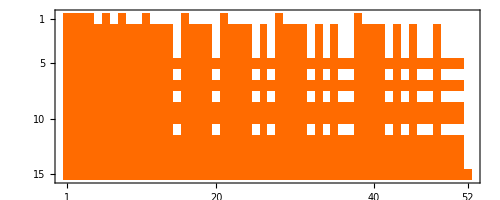

```mathematica
Table[If[IGSubisomorphicQ[allGraphs4[k,"graph"],allGraphs5[l,"graph"]],1,0],{k,allGraphs4AtomKeys},{l,allGraphs5AtomKeys}]//MatrixPlot
```

```mathematica
Information[IGSubisomorphicQ]
```

IGSubisomorphicQ[subgraph, graph] tests if subgraph is contained within graph.

Attributes[IGSubisomorphicQ]={Protected,ReadProtected}
 
SyntaxInformation[IGSubisomorphicQ]={ArgumentsPattern→{_,_}}

```mathematica
Table[If[IGSubisomorphicQ[allGraphs5[k,"graph"],allGraphs5[l,"graph"]],1,0],{k,Sort[allGraphs5AtomKeys]},{l,Sort[allGraphs5AtomKeys]}]//
```

5

```mathematica
Table[If[IGSubisomorphicQ[allGraphs5[k,"graph"],allGraphs5[k,"graph"]],1,0],{k,allGraphs5AtomKeys}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Table[If[IGSubisomorphicQ[allGraphs4[k,"graph"],allGraphs5[l,"graph"]],{allGraphs4[k,"atleast"],allGraphs5[l,"atleast"]},0],{k,allGraphs4AtomKeys},{l,allGraphs5AtomKeys}]
```

{{{0,0},{0,0},{0,1},{0,0},0,{0,1},0,{0,1},0,0,{0,0},0,0,0,0,{0,0},0,0,0,0,{0,1},0,0,0,0,0,0,{0,1},0,0,0,0,0,0,0,0,0,{0,0},0,0,0,0,0,0,0,0,0,0,0,0,0,0},{{1,0},{1,0},{1,1},{1,0},{1,1},{1,1},{1,0},{1,1},{1,0},{1,0},{1,0},{1,1},{1,0},{1,1},0,{1,0},{1,1},{1,0},{1,1},0,{1,1},{1,0},{1,0},{1,0},0,{1,1},0,{1,1},{1,0},{1,0},{1,0},0,{1,0},0,{1,0},0,0,{1,0},{1,1},{1,0},{1,1},0,{1,1},0,{1,0},0,0,{1,1},0,0,0,0},{{0,0},{0,0},{0,1},{0,0},{0,1},{0,1},{0,0},{0,1},{0,0},{0,0},{0,0},{0,1},{0,0},{0,1},0,{0,0},{0,1},{0,0},{0,1},0,{0,1},{0,0},{0,0},{0,0},0,{0,1},0,{0,1},{0,0},{0,0},{0,0},0,{0,0},0,{0,0},0,0,{0,0},{0,1},{0,0},{0,1},0,{0,1},0,{0,0},0,0,{0,1},0,0,0,0},{{1,0},{1,0},{1,1},{1,0},{1,1},{1,1},{1,0},{1,1},{1,0},{1,0},{1,0},{1,1},{1,0},{1,1},0,{1,0},{1,1},{1,0},{1,1},0,{1,1},{1,0},{1,0},{1,0},0,{1,1},0,{1,1},{1,0},{1,0},{1,0},0,{1,0},0,{1,0},0,0,{1,0},{1,1},{1,0},{1,1},0,{1,1},0,{1,0},0,0,{1,1},0,0,0,0},{{1,0},{1,0},{1,1},{1,0},{1,1},{1,1},{1,0},{1,1},{1,0},{1,0},{1,0},{1,1},{1,0},{1,1},{1,1},{1,0},{1,1},{1,0},{1,1},{1,1},{1,1},{1,0},{1,0},{1,0},{1,0},{1,1},{1,1},{1,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,1},{1,0},{1,1},{1,0},{1,1},{1,1},{1,1},{1,1},{1,0},{1,0},{1,1},{1,1},{1,1},{1,1},{1,1},0},{{1,0},{1,0},{1,1},{1,0},{1,1},{1,1},{1,0},{1,1},{1,0},{1,0},{1,0},{1,1},{1,0},{1,1},0,{1,0},{1,1},{1,0},{1,1},0,{1,1},{1,0},{1,0},{1,0},0,{1,1},0,{1,1},{1,0},{1,0},{1,0},0,{1,0},0,{1,0},0,0,{1,0},{1,1},{1,0},{1,1},0,{1,1},0,{1,0},0,0,{1,1},0,0,0,0},{{1,0},{1,0},{1,1},{1,0},{1,1},{1,1},{1,0},{1,1},{1,0},{1,0},{1,0},{1,1},{1,0},{1,1},{1,1},{1,0},{1,1},{1,0},{1,1},{1,1},{1,1},{1,0},{1,0},{1,0},{1,0},{1,1},{1,1},{1,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,1},{1,0},{1,1},{1,0},{1,1},{1,1},{1,1},{1,1},{1,0},{1,0},{1,1},{1,1},{1,1},{1,1},{1,1},0},{{0,0},{0,0},{0,1},{0,0},{0,1},{0,1},{0,0},{0,1},{0,0},{0,0},{0,0},{0,1},{0,0},{0,1},0,{0,0},{0,1},{0,0},{0,1},0,{0,1},{0,0},{0,0},{0,0},0,{0,1},0,{0,1},{0,0},{0,0},{0,0},0,{0,0},0,{0,0},0,0,{0,0},{0,1},{0,0},{0,1},0,{0,1},0,{0,0},0,0,{0,1},0,0,0,0},{{0,0},{0,0},{0,1},{0,0},{0,1},{0,1},{0,0},{0,1},{0,0},{0,0},{0,0},{0,1},{0,0},{0,1},{0,1},{0,0},{0,1},{0,0},{0,1},{0,1},{0,1},{0,0},{0,0},{0,0},{0,0},{0,1},{0,1},{0,1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,1},{0,0},{0,1},{0,0},{0,1},{0,1},{0,1},{0,1},{0,0},{0,0},{0,1},{0,1},{0,1},{0,1},{0,1},0},{{1,0},{1,0},{1,1},{1,0},{1,1},{1,1},{1,0},{1,1},{1,0},{1,0},{1,0},{1,1},{1,0},{1,1},{1,1},{1,0},{1,1},{1,0},{1,1},{1,1},{1,1},{1,0},{1,0},{1,0},{1,0},{1,1},{1,1},{1,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,1},{1,0},{1,1},{1,0},{1,1},{1,1},{1,1},{1,1},{1,0},{1,0},{1,1},{1,1},{1,1},{1,1},{1,1},0},{{1,0},{1,0},{1,1},{1,0},{1,1},{1,1},{1,0},{1,1},{1,0},{1,0},{1,0},{1,1},{1,0},{1,1},0,{1,0},{1,1},{1,0},{1,1},0,{1,1},{1,0},{1,0},{1,0},0,{1,1},0,{1,1},{1,0},{1,0},{1,0},0,{1,0},0,{1,0},0,0,{1,0},{1,1},{1,0},{1,1},0,{1,1},0,{1,0},0,0,{1,1},0,0,0,0},{{1,0},{1,0},{1,1},{1,0},{1,1},{1,1},{1,0},{1,1},{1,0},{1,0},{1,0},{1,1},{1,0},{1,1},{1,1},{1,0},{1,1},{1,0},{1,1},{1,1},{1,1},{1,0},{1,0},{1,0},{1,0},{1,1},{1,1},{1,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,1},{1,0},{1,1},{1,0},{1,1},{1,1},{1,1},{1,1},{1,0},{1,0},{1,1},{1,1},{1,1},{1,1},{1,1},0},{{1,0},{1,0},{1,1},{1,0},{1,1},{1,1},{1,0},{1,1},{1,0},{1,0},{1,0},{1,1},{1,0},{1,1},{1,1},{1,0},{1,1},{1,0},{1,1},{1,1},{1,1},{1,0},{1,0},{1,0},{1,0},{1,1},{1,1},{1,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,1},{1,0},{1,1},{1,0},{1,1},{1,1},{1,1},{1,1},{1,0},{1,0},{1,1},{1,1},{1,1},{1,1},{1,1},0},{{1,0},{1,0},{1,1},{1,0},{1,1},{1,1},{1,0},{1,1},{1,0},{1,0},{1,0},{1,1},{1,0},{1,1},{1,1},{1,0},{1,1},{1,0},{1,1},{1,1},{1,1},{1,0},{1,0},{1,0},{1,0},{1,1},{1,1},{1,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,1},{1,0},{1,1},{1,0},{1,1},{1,1},{1,1},{1,1},{1,0},{1,0},{1,1},{1,1},{1,1},{1,1},{1,1},0},{{1,0},{1,0},{1,1},{1,0},{1,1},{1,1},{1,0},{1,1},{1,0},{1,0},{1,0},{1,1},{1,0},{1,1},{1,1},{1,0},{1,1},{1,0},{1,1},{1,1},{1,1},{1,0},{1,0},{1,0},{1,0},{1,1},{1,1},{1,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,1},{1,0},{1,1},{1,0},{1,1},{1,1},{1,1},{1,1},{1,0},{1,0},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}}}

```mathematica
allGraphs4[365,"compwhy"]
```

This is a planar contraction

```mathematica
Delete5[set_]:=Select[Map[Select[#,#≠5&]&,set],#≠{}&]
```

```mathematica
allGraphs5[alfa1Key,"vertexsets"]
```

{{1,3},{2,4},{5}}

```mathematica
Delete5[allGraphs5[alfa1Key,"vertexsets"]]
```

{{1,3},{2,4}}

```mathematica
Map[
{ShowGraph4Least[#[[1]]],ShowGraph5Least[#[[2]]]}&,
Select[
Flatten[Table[{k,l},{k,allGraphs4AtomKeys},{l,allGraphs5AtomKeys}],1],
allGraphs4[#[[1]],"vertexsets"]==Delete5[allGraphs5[#[[2]],"vertexsets"]]&&
IGSubisomorphicQ[allGraphs4[#[[1]],"graph"],allGraphs5[#[[2]],"graph"]]&&
allGraphs4[#[[1]],"atleast"]>allGraphs5[#[[2]],"atleast"]&
]]
```

{{-Graphics-3651,-Graphics-295330},{-Graphics-3651,-Graphics-295600},{-Graphics-3731,-Graphics-297670},{-Graphics-3731,-Graphics-297970},{-Graphics-3911,-Graphics-317140},{-Graphics-3911,-Graphics-317380},{-Graphics-4001,-Graphics-319540},{-Graphics-4001,-Graphics-319840},{-Graphics-4731,-Graphics-382810},{-Graphics-4731,-Graphics-383080},{-Graphics-6071,-Graphics-492070},{-Graphics-6071,-Graphics-492100},{-Graphics-6371,-Graphics-514750},{-Graphics-6371,-Graphics-514780}}